```mathematica
Exit[]
```

```mathematica
a={1,2,3,4,5};A=4;
```

```mathematica
p[i_,x_]:=Exp[(a[[i]]-A)*x]
```

```mathematica
NSolve[Sum[p[i,x],{i,1,5}]==6,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.69866-2.20459 ⅈ},{x→-0.69866+2.20459 ⅈ},{x→-0.157612},{x→1.55493}}

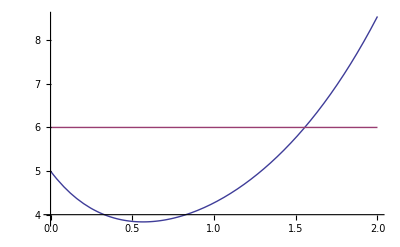

```mathematica
Plot[{Sum[p[i,x],{i,1,5}],6},{x,0,2}]
```